```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Lab21_data.xlsx"][[1]];
```

## Calculating Klein-Cook parameter

Data from XLSX file:

```mathematica
TableView[data]
```

Диапазон частотРасстояние до экрана1 МГц100 МГц130 МГц100 смНахождение скорости звукаЧастота, МГцРасстояние от нулевого максимума, смУгол в радианахЧастота^2, МГц^2Синус углаДлина волны в нмСкорость звука80.1.50.01499896400.0.014998321669.11733.52832236581790.1.70.01699848100.0.016997519120.41720.836842333556295.1.80.01799819025.0.017997118058.51715.5556302735483100.1.90.018997710000.0.018996617108.41710.8350379298147105.1.950.019497511025.0.019496316669.81750.332687126936110.2.0.019997312100.0.01999616253.21787.8574642571482115.2.10.020996913225.0.020995415479.61780.1542990052078120.2.20.021996514400.0.021994714776.31773.1562208308308125.2.350.023495715625.0.023493513833.61729.2006821202392130.2.40.023995416900.0.023993113545.61760.9235936796856Скорость звука1746.2380779922782Напряжение0.3.80.381.2.20.222.0.60.06-1.1.60.16-2.0.20.02Напряжение генератораЧастотаМощность нулевогоМощность первого7.45.1`*^3.40000000000000002`.17999999999999999`1.11005.44999999999999996`13.55105..40000000000000002`.17000000000000001`3.67205.42499999999999999`13.34.11`*^3.40000000000000002`.12`3.55911.29999999999999999`16.45115..40000000000000002`.080000000000000002`5.41205.19999999999999998`19.7.12`*^3.40000000000000002`.050000000000000003`7.7618.125`Null125..40000000000000002`.014999999999999999`4.2632.037499999999999999`

Klein-Cook parameter function:

```mathematica
Q[λ_,L_,f_,n_,v_]:=(2π λ L f^2)/(n v^2);
```

Extracting necessary values from table:

```mathematica
vals=<|
f-> Quantity[data[[6;;15,1]],"Megahertz"],
v-> Quantity[data[[6;;15,7]],"Meters"/"Seconds"],
n-> Table[2.38,Length[data[[6;;15,1]]]](*From open sources*),
λ-> Table[Quantity[650,"Nanometers"],Length[data[[6;;15,1]]]](*From experiment*),
L->Table[Quantity[1,"Centimeters"],Length[data[[6;;15,1]]]](*From experiment*)
|>;
```

Calculating Klein - Cook parameter for each measurement:

```mathematica
KleinCook=UnitSimplify[Q@@{vals[λ],vals[L],vals[f],vals[n],vals[v]}];
KleinCook//TableForm
```

36.5455
46.9377
52.6204
58.6273
61.7524
64.9585
71.6138
78.5932
89.6697
93.5238

```mathematica
Export["KC.xlsx",QuantityMagnitude[Transpose[{vals[f],KleinCook}]]];
```

## Calculating ρ value

ρ-function:

```mathematica
ρ[K_,n_,k_,Δn_]:=K^2/(k^2 Δn n);
```

Extracting values:

```mathematica
valsρ=<|
K-> (2π)/Quantity[data[[6;;15,6]],"Nanometers"],
n-> vals[n],
k-> (2π)/vals[λ],
Δn-> Table[10^-4,Length[data[[6;;15,1]]]]
|>;
```

```mathematica
ρvals=UnitSimplify[ρ@@{valsρ[K],valsρ[n],valsρ[k],valsρ[Δn]}]
```

{3.78066,4.85574,5.44361,6.06504,6.38833,6.72,7.4085,8.13052,9.27639,9.6751}

```mathematica
Export["rho.xlsx",QuantityMagnitude[Transpose[{vals[f],ρvals}]]];
```

## Radiation power distribution in Raman - Nat diffraction maximums

We only have to plot the data from .xlsx spreadsheet:

```mathematica
pwrdstrmax = Max[data[[19;;23,3]]];
pwrdstr=Transpose[{data[[19;;23,1]],data[[19;;23,3]]/pwrdstrmax}];
```

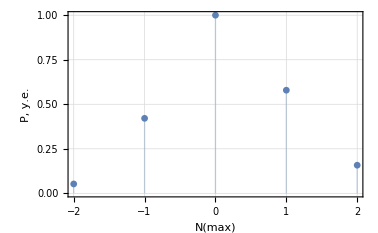

```mathematica
dstplt=ListPlot[pwrdstr,Filling->Axis,PlotTheme->"Detailed",FrameLabel->{"N(max)","P, у.е."}]
```

```mathematica
Export["dstplt.png",dstplt,ImageResolution->{1920,1440}];
```

## Plotting I'/I_0(P)

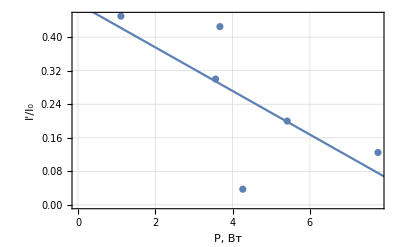

```mathematica
pltdata=data[[35;;41,5;;6]];
pltfit=LinearModelFit[pltdata,x,x];
plt=Show[
ListPlot[
pltdata,
PlotTheme->"Detailed",
FrameLabel->{"P, Вт", "I'/I_0"}
],
Plot[
pltfit["BestFit"],{x,0,8}
]
]
```

```mathematica
Export["plt.png",plt,ImageResolution->{1920,1440}];
```

```mathematica
pltfit["BestFit"]
```

0.479585-0.0519821 x